# Funcion de correlacion

```mathematica
1+1;
SetDirectory[NotebookDirectory[]];
```

```mathematica
data=Import["data.csv","Table","FieldSeparators"-> ","];
```

$Aborted

```mathematica
data//TableForm;
```

```mathematica
Col1=data[[All,2]];
```

```mathematica
Col2=data[[All,3]];
```

```mathematica
Col3=data[[All,9]];
```

```mathematica
Col4=data[[All,6]];
```

```mathematica
ndata=Length[data];
```

```mathematica
c=1 (*km/s*)
H0=100(*h km/(s Mpc)*);
```

1

```mathematica
Min[data[[All,6]]]
```

Min[-9999,rmag]

```mathematica
a=Select[data,(17<#[[6]]<18)&];
```

```mathematica
Length[a]
```

54168

```mathematica
Length[Col4]
```

1792114

### escogiendo bins

#### bins

```mathematica
bin1=Select[data,(0<#[[9]]<0.2)&];
bin2=Select[data,(0.2<#[[9]]<0.4)&];
bin3=Select[data,(0.4<#[[9]]<0.6)&];
bin4=Select[data,(0.6<#[[9]]<0.8)&];
bin5=Select[data,(0.8<#[[9]]<1.0)&];
bin6=Select[data,(1.0<#[[9]]<1.2)&];
bin7=Select[data,(1.2<#[[9]]<1.4)&];
bin8=Select[data,(1.4<#[[9]]<1.6)&];
bin9=Select[data,(1.6<#[[9]]<1.8)&];
bin10=Select[data,(1.8<#[[9]]<2.01)&];
```

#### longitud bins

```mathematica
Length[bin1]
```

92259

```mathematica
Length[bin2]
```

306502

```mathematica
Length[bin3]
```

815242

```mathematica
Length[bin4]
```

418754

```mathematica
Length[bin5]
```

135184

```mathematica
Length[bin6]
```

18776

```mathematica
Length[bin7]
```

4009

```mathematica
Length[bin8]
```

1124

```mathematica
Length[bin9]
```

193

```mathematica
Length[bin10]
```

67

## distancias:

### bin1

#### columnas

```mathematica
Clear[col1,col2,col3];
col1=bin1[[All,2]];
col2=bin1[[All,3]];
col3=bin1[[All,9]];
```

#### distancia con redshift

```mathematica
For[i=1,i≤100,i++,For[j=1,j≤100,j++,dist1=Table[If[i≠j,(ArcCos[Sin[col1[[i]]]*Sin[col1[[j]]]+Cos[col1[[i]]]*Cos[col1[[j]]*Cos[col2[[i]]-col2[[j]]]]])*c/(2*H0(1+(col3[[i]]-col3[[j]]))) ,Nothing],{i,1,100},{j,1,100}]]]
```

```mathematica
Export["dist1.dat",dist1];
```

```mathematica
d1=Import["dist1.dat","Table"];
```

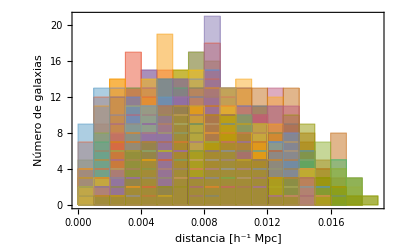

```mathematica
h1=Histogram[d1,Frame->{{True,False},{True,False}}, FrameLabel->{{"Número de galaxias",None},{"distancia [h^-1 Mpc]",None}}]
```

```mathematica
Export["h1.png",h1];
```

```mathematica
coldr=RandomSample[col1];
```

```mathematica
For[i=1,i≤100,i++,For[j=1,j≤100,j++,dist1dr=Table[If[i≠j,(ArcCos[Sin[coldr[[i]]]*Sin[coldr[[j]]]+Cos[coldr[[i]]]*Cos[coldr[[j]]*Cos[col2[[i]]-col2[[j]]]]])*c/(2*H0*(1+(col3[[i]]-col3[[j]]))),Nothing],{i,1,100},{j,1,100}]]]
```

```mathematica
Export["dist1dr.dat",dist1dr];
```

```mathematica
d2=Import["dist1dr.dat","Table"];
```

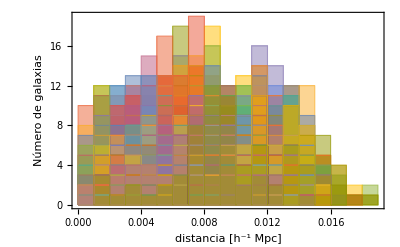

```mathematica
h2=Histogram[d2,Frame->{{True,False},{True,False}}, FrameLabel->{{"Número de galaxias",None},{"distancia [h^-1 Mpc]",None}}]
```

```mathematica
Export["h2.png",h2];
```

```mathematica
colrr=RandomSample[col2];
```

```mathematica
For[i=1,i≤100,i++,For[j=1,j≤100,j++,dist1rr=Table[If[i≠j,(ArcCos[Sin[coldr[[i]]]*Sin[coldr[[j]]]+Cos[coldr[[i]]]*Cos[coldr[[j]]*Cos[colrr[[i]]-colrr[[j]]]]])*c/(2*H0*(1+(col3[[i]]-col3[[j]]))),Nothing],{i,1,100},{j,1,100}]]]
```

```mathematica
Export["dist1rr.dat",dist1rr];
```

```mathematica
d3=Import["dist1rr.dat","Table"];
```

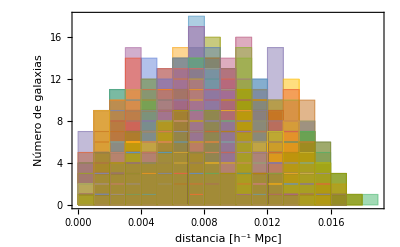

```mathematica
h3=Histogram[d3,Frame->{{True,False},{True,False}}, FrameLabel->{{"Número de galaxias",None},{"distancia [h^-1 Mpc]",None}}]
```

```mathematica
Export["h3.png",h3];
```

```mathematica
w1=(d1-2*d2+d3)/d3;
```

```mathematica
Export["w1.dat",w1];
```

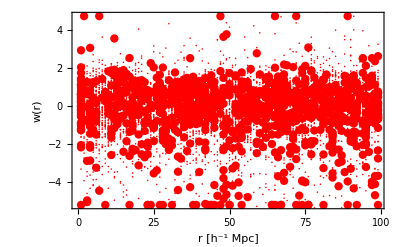

```mathematica
ListPlot[w1,Mesh->All, AxesOrigin->{0,0},Axes-> False, Frame->{{True,False},{True,False}}, FrameLabel->{{"w(r)",None},{"r [h^-1 Mpc]",None}}, FrameTicks->All,ImageSize->400, PlotStyle->Red,LabelStyle->{16,GrayLevel[0],Bold}]
```

### bin10

#### columnas

```mathematica
Clear[col1,col2,col3];
col1=bin10[[All,2]];
col2=bin10[[All,3]];
col3=bin10[[All,9]];
```

#### distancia con redshift

```mathematica
For[i=1,i≤Length[bin10],i++,For[j=1,j≤Length[bin10],j++,dist10=Table[If[i≠j,(ArcCos[Sin[col1[[i]]]*Sin[col1[[j]]]+Cos[col1[[i]]]*Cos[col1[[j]]*Cos[col2[[i]]-col2[[j]]]]])*c/(2*H0(1+(col3[[i]]-col3[[j]]))) ,Nothing],{i,1,Length[bin10]},{j,1,Length[bin10]}]]]
```

```mathematica
Export["dist10.dat",dist10];
```

```mathematica
d4=Import["dist10.dat","Table"];
```

```mathematica
h4=Histogram[d4,Frame->{{True,False},{True,False}}, FrameLabel->{{"Número de galaxias",None},{"distancia [h^-1 Mpc]",None}}]
Export["d4.png",h4];
```

-Graphics-

```mathematica
coldr=RandomSample[col1];
```

```mathematica
For[i=1,i≤Length[bin10],i++,For[j=1,j≤Length[bin10],j++,dist10dr=Table[If[i≠j,(ArcCos[Sin[coldr[[i]]]*Sin[coldr[[j]]]+Cos[coldr[[i]]]*Cos[coldr[[j]]*Cos[col2[[i]]-col2[[j]]]]])*c/(2*H0*(1+(col3[[i]]-col3[[j]]))),Nothing],{i,1,Length[bin10]},{j,1,Length[bin10]}]]]
```

```mathematica
Export["dist10dr.dat",dist10dr];
```

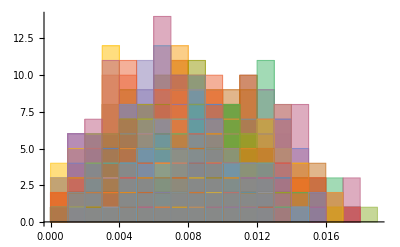

```mathematica
d5=Import["dist10dr.dat","Table"];
h5=Histogram[d4,Frame->{{True,False},{True,False}}, FrameLabel->{{"Número de galaxias",None},{"distancia [h^-1 Mpc]",None}}]
Export["d5.png",h5];
```

```mathematica
colrr=RandomSample[col2];
```

```mathematica
For[i=1,i≤Length[bin10],i++,For[j=1,j≤Length[bin10],j++,dist10rr=Table[If[i≠j,(ArcCos[Sin[coldr[[i]]]*Sin[coldr[[j]]]+Cos[coldr[[i]]]*Cos[coldr[[j]]*Cos[colrr[[i]]-colrr[[j]]]]])*c/(2*H0*(1+(col3[[i]]-col3[[j]]))),Nothing],{i,1,Length[bin10]},{j,1,Length[bin10]}]]]
```

```mathematica
Export["dist10rr.dat",dist10rr];
```

```mathematica
Import["dist10rr.dat","Table"];
```

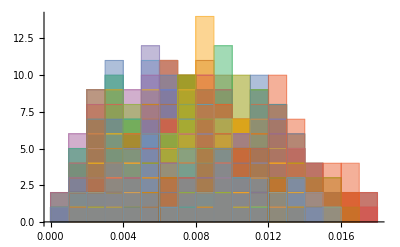

```mathematica
d6=Import["dist10dr.dat","Table"];
h6=Histogram[d6,Frame->{{True,False},{True,False}}, FrameLabel->{{"Número de galaxias",None},{"distancia [h^-1 Mpc]",None}}]
Export["d6.png",h6];
```

```mathematica
w10=(dist10-2*dist10dr+dist10rr)/dist10rr;
```

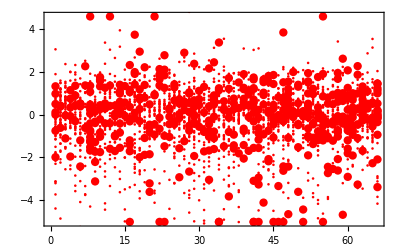

```mathematica
ListPlot[w10,Mesh->All, AxesOrigin->{0,0},Axes-> False, Frame->{{True,False},{True,False}}, FrameTicks->All,ImageSize->400, PlotStyle->Red,LabelStyle->{16,GrayLevel[0],Bold}]
```